```mathematica
ClearAll["Global`*"]
```

# 1) Loading Tables

```mathematica
(*rawArray10=Table[ BinaryReadList["WallHeight"<>ToString[i]<>" - rho=0.1.float", "Real32"],{i,startBounce,endBounce}];
bounces10 = Table[Table[{(i-1)/(tableSize-1),rawArray10[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];

rawArray20=Table[ BinaryReadList["WallHeight"<>ToString[i]<>" - rho=0.2.float", "Real32"],{i,startBounce,endBounce}];
bounces20 = Table[Table[{(i-1)/(tableSize-1),rawArray20[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];

rawArray30=Table[ BinaryReadList["WallHeight"<>ToString[i]<>" - rho=0.3.float", "Real32"],{i,startBounce,endBounce}];
bounces30 = Table[Table[{(i-1)/(tableSize-1),rawArray30[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];

rawArray40=Table[ BinaryReadList["WallHeight"<>ToString[i]<>" - rho=0.4.float", "Real32"],{i,startBounce,endBounce}];
bounces40 = Table[Table[{(i-1)/(tableSize-1),rawArray40[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];

rawArray50=Table[ BinaryReadList["WallHeight"<>ToString[i]<>" - rho=0.5.float", "Real32"],{i,startBounce,endBounce}];
bounces50 = Table[Table[{(i-1)/(tableSize-1),rawArray50[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];

rawArray60=Table[ BinaryReadList["WallHeight"<>ToString[i]<>" - rho=0.6.float", "Real32"],{i,startBounce,endBounce}];
bounces60 = Table[Table[{(i-1)/(tableSize-1),rawArray60[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];

rawArray70=Table[ BinaryReadList["WallHeight"<>ToString[i]<>" - rho=0.7.float", "Real32"],{i,startBounce,endBounce}];
bounces70 = Table[Table[{(i-1)/(tableSize-1),rawArray70[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];

rawArray80=Table[ BinaryReadList["WallHeight"<>ToString[i]<>" - rho=0.8.float", "Real32"],{i,startBounce,endBounce}];
bounces80 = Table[Table[{(i-1)/(tableSize-1),rawArray80[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];

rawArray90=Table[ BinaryReadList["WallHeight"<>ToString[i]<>" - rho=0.9.float", "Real32"],{i,startBounce,endBounce}];
bounces90 = Table[Table[{(i-1)/(tableSize-1),rawArray90[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];

rawArray100=Table[ BinaryReadList["WallHeight"<>ToString[i]<>".float", "Real32"],{i,startBounce,endBounce}];
bounces100 = Table[Table[{(i-1)/(tableSize-1),rawArray100[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];

allBounces={bounces10,bounces20,bounces30,bounces40,bounces50,bounces60,bounces70,bounces80,bounces90,bounces100};*)
```

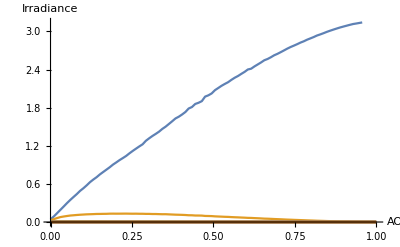
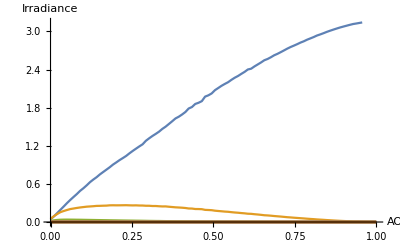
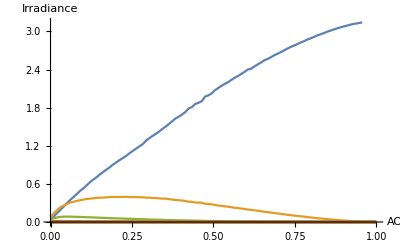
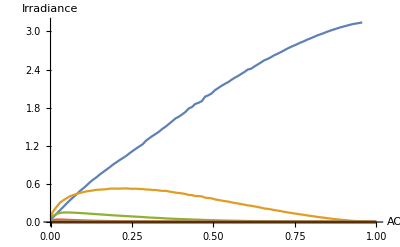
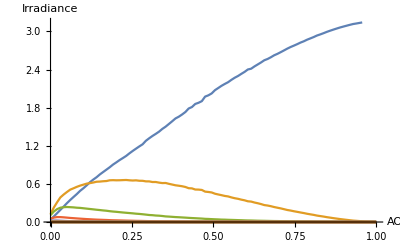
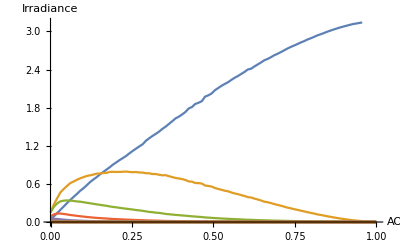
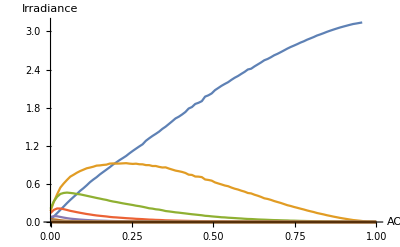
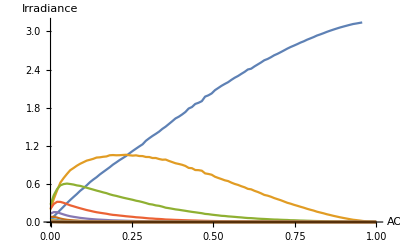

```mathematica
SetDirectory[NotebookDirectory[]]; 
tableSize =samplesCount= 100;
bouncesCount = 21;
startBounce=0;
endBounce=bouncesCount-1;

loadBounce[ρ_]:=Module[{},
rawArray=Table[ BinaryReadList["WallHeight"<>ToString[i]<>" - rho=0."<>ToString[ρ]<>".float", "Real32"],{i,startBounce,endBounce}];
 Table[Table[{(i-1)/(tableSize-1),rawArray[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}]
];

rawArray100=Table[ BinaryReadList["WallHeight"<>ToString[i]<>".float", "Real32"],{i,startBounce,endBounce}];
bounces100 = Table[Table[{(i-1)/(tableSize-1),rawArray100[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];
ListLinePlot[bounces100,PlotRange->{0,π}];

someBounces=Table[loadBounce[ρ],{ρ,1,9}];
allBounces=Append[ someBounces,bounces100];

Table[ListLinePlot[allBounces[[rhoIndex]],PlotRange->{0,π},AxesLabel->{"AO","Irradiance"}],{rhoIndex,1,10}]
```

Let’s sum all tables for each ρ

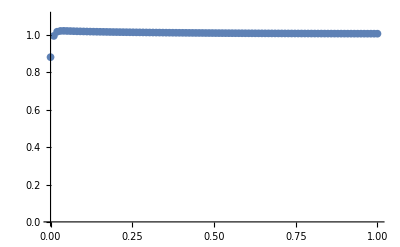

```mathematica
ρ=10;
ListPlot[Table[{(i-1)/(tableSize-1), ρ/(10*π)*(allBounces[[ρ]][[1]][[i]][[2]] + Sum[allBounces[[ρ]][[b]][[i]][[2]] ,{b,2,bouncesCount}])},{i,1,tableSize}],PlotRange->{0,1.1}]
```

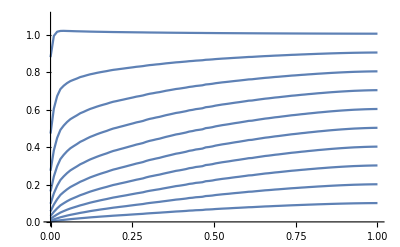

```mathematica
sumBounces=Table[Table[{(i-1)/(tableSize-1), ρ/(10*π)*(allBounces[[ρ]][[1]][[i]][[2]] + Sum[allBounces[[ρ]][[b]][[i]][[2]] ,{b,2,bouncesCount}])},{i,1,tableSize}],{ρ,1,10}];
Show[
Table[ListLinePlot[sumBounces[[ρ]],PlotRange->{0,1.1}],{ρ,1,10}]
]
```

# 2) Establishing Analytical Model

Simplify F0=α if needed!

```mathematica
F0[α_]:=α*(1+0.5*(1-α)^0.75)
E0[α_]:=π*α    (* Simpler *)
E0[α_]:=π*F0[α]
E1[α_]:=86.635502983679205*α*(1-α)^1.5 Exp[-3.3364392003423804*√(√α)]
tau[α_]:=1-E1[α]/Max[0.01,π-E0[α]]
tau[0.5]
```

0.160973

We can also simplify some expressions by removing the π factor:

```mathematica
Show[
Plot[Exp[-3.3364392003423804*√(√α)],{α,0,1}],
Plot[2^(-3.3364392003423804/Log[2]*√(√α)),{α,0,1},PlotStyle->Red]
];
```

```mathematica
Clear[E0,E1,F0,F1]
(*F0[α_]:=α*(1+0.5*(1-α)^0.75)
E1[α_]:=27.576937094210384876503293303541*α*(1-α)^1.5*2^(-3.3364392003423804/Log[2]*√(√α))
tau[α_]:=1-E1[α]/Max[0.0001,1-F0[α]]
*)
F0[α_]=α*(1+(1-α)^0.75/2)
F1[α_]:=27.576937094210384876503293303541*α*(1-α)^1.5 Exp[-3.3364392003423804*√(√α)];
tau[α_]:=1-F1[α]/Max[0.001,1-F0[α]];


tau[α_]:=1-F1[α]/(1/100 + Clip[1-F0[α]])
```

(1+1/2 (1-α)^0.75) α

```mathematica
Plot[√((1-α)^1.5),{α,0,1}];
Plot[(1-α)^0.75,{α,0,1}];
```

# 3) Comparing Experiment and Model

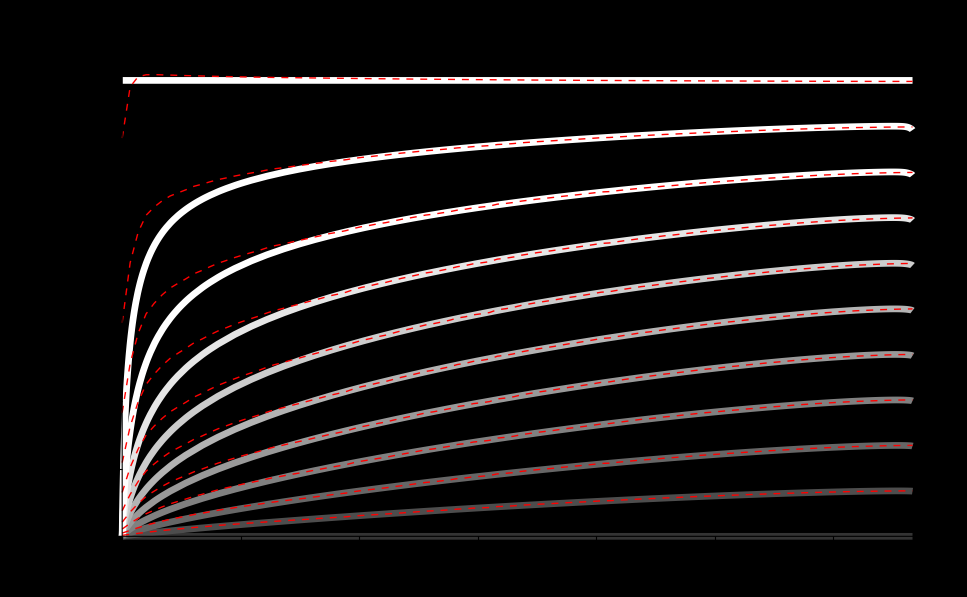

```mathematica
Show[
Table[Plot[ρ/π * π*(F0[α]+ F1[α]*ρ/(1-ρ*tau[α])),{α,0,1},PlotRange->{0,1.1},PlotStyle->{GrayLevel[ρ+0.2],Thickness-> 0.005},Background->Black,AxesLabel->{"AO","Outgoing Radiance"},LabelStyle->White],{ρ,0,1,0.1}],
Table[
ListLinePlot[sumBounces[[ρ]],PlotRange->{0,1.1},PlotStyle->{Dashed,Thin,Red},Background->Black]
,{ρ,1,10}]
]
```

```mathematica
(*Show[Plot[2^(2x),{x,0,1},PlotStyle->Thick],Plot[(2^x)^2,{x,0,1},PlotStyle->Red]]*)
```